```mathematica
parameters= {T0-> 78.3,a-> 1.696×10^6,b-> -3.422×10^9,c-> 1.797×10^11,d-> 3.214×10^12,ρBaTiO3-> 6.02×10^3};
```

```mathematica
F=(a(T-T0))/2 P^2+b/4 P^4+c/6 P^6-E0 P;
```

## P(T)

```mathematica
Clear[E0, D1]
D1:=D[F, {P,1}]
```

```mathematica
Solve[D1==0/.E0-> 0, P]
```

{{P→0},{P→-(√(-b/c-(√(b^2-4 a c T+4 a c T0))/c))/(√2)},{P→(√(-b/c-(√(b^2-4 a c T+4 a c T0))/c))/(√2)},{P→-(√(-b/c+(√(b^2-4 a c T+4 a c T0))/c))/(√2)},{P→(√(-b/c+(√(b^2-4 a c T+4 a c T0))/c))/(√2)}}

```mathematica
(*find out T1*)
FindRoot[D1==0/.P->√((-b+√(b^2-4 a c (T-T0)))/(2c))/.parameters/.T->Tc,{Tc,80}]
```

{Tc→84.4024}

```mathematica
Clear[Ps2]
Ps2 = (-b+√(b^2-4 a c (T-T0)))/(2c);
```

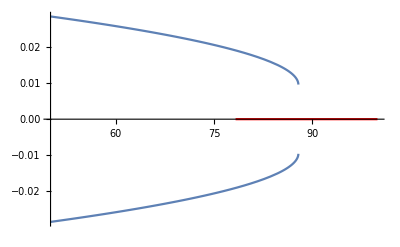

```mathematica
Show[Plot[Ps2/.parameters,{T, 50,100}],Plot[-Ps2/.parameters,{T, 50,100}], Plot[0,{T,78.3,100},PlotStyle->Red],AxesOrigin->{50,0},PlotRange-> All]
```

```mathematica
D1=D[F, {P,1}]
```

-E0+b P^3+c P^5+a P (T-T0)

```mathematica
Plot[Solve[-E0+b P^3+c P^5+a P (T-T0)==0],E0 -> 10,T]
```

Plot::nonopt: Options expected (instead of T) beyond position 2 in Plot[Solve[-E0+b P^3+c P^5+a P (T-T0)==0],E0→10,T]. An option must be a rule or a list of rules.

Plot[Solve[-E0+b P^3+c P^5+a P (T-T0)==0],E0→10,T]

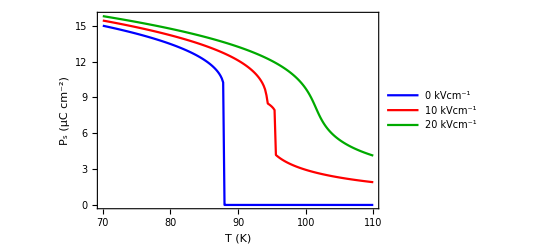

```mathematica
Clear[E0]
Tiin=70;Tfin=110;NoPin=200;
E0Range=Range[0,20,10];
PsEqs[E0_,T_]:=Ps/.FindRoot[-e0+b Ps^3+c Ps^5+a Ps (T-T0)/.parameters/.e0-> E0×10^5,{Ps,0.15,0,50}]//Quiet
PsTable[E0_,Ti_,Tf_,NoP_]:=ParallelTable[{T,10^2 PsEqs[E0,T]},{T,Ti,Tf,(Tf-Ti)/NoP}]
Psdata=PsTable[#,Tiin,Tfin,NoPin]&/@E0Range;
ListPlot[Psdata,Joined->True,Frame->True,FrameTicksStyle->Directive[15],FrameStyle-> Black,FrameLabel-> {Style["T (K)",{15,SingleLetterItalics->False}],Style["P_s (μC cm^-2)",15],None},PlotLegends->{"0 kVcm^-1","10 kVcm^-1","20 kVcm^-1"},PlotStyle->{Blue,Red,Darker[Green]}]
```

## Dielectric constant and Susceptibility (1/k)

```mathematica
Clear[E1]
E1= a P (T-T0)+b P^3+c P^5;
k_inverse = D[E1,{P,1}]
k= (D[E1,{P,1}])^-1
```

3 b P^2+5 c P^4+a (T-T0)

1/(3 b P^2+5 c P^4+a (T-T0))

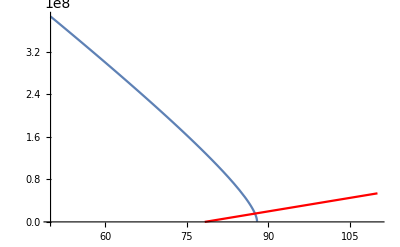

```mathematica
Show[Plot[3 b P^2+5 c P^4+a (T-T0)/. P->(√(-b/c+(√(b^2-4 a c T+4 a c T0))/c))/(√2) /.parameters,{T, 50,100}], Plot[a (T-T0)/.parameters, {T, 78.3,110}, PlotStyle->Red], PlotRange-> All]
```

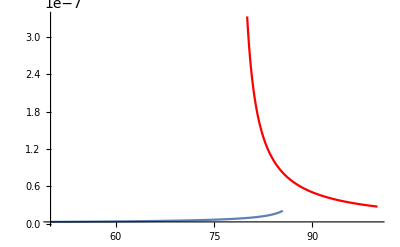

```mathematica
Show[Plot[1/(3 b P^2+5 c P^4+a (T-T0))/. P->(√(-b/c+(√(b^2-4 a c T+4 a c T0))/c))/(√2) /.parameters,{T, 50,100}], Plot[1/(a (T-T0))/.parameters, {T, 78.3,100}, PlotStyle->Red], PlotRange-> All]
```

```mathematica
Clear[A]
A =F-E0*P
dS=-D[A, {T,1}]
```

-E0 P+(b P^4)/4+(c P^6)/6+1/2 a P^2 (T-T0)